# 1. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijske smeri: Aplikativna fizika, Praktična matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita so tri naloge, ki so skupaj vredne 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [10 točk]

1. (5 točk) Izračunajte vrsto .
 2. (5 točk) Izračunajte integral

```mathematica
Sum[1/n^2,{n,1,Infinity}]
Integrate[Sqrt[x/(1-x)],{x,0,1}]
```

π^2/6

π/2

## 2. naloga [10 točk]

1. (5 točk) Definirajte funkcijo  f, ki sprejme parametra x in y in ima predpis .
2. (5 točk) Narišite graf implicitno podane funkcije, ko je   za  in  . Uporabite funkcijo   ContourPlot.

```mathematica
ClearAll[x,y,f]
```

```mathematica
f[x_,y_]:=(x^2+y^2)^2-y^2-x (x^2+y^2);
```

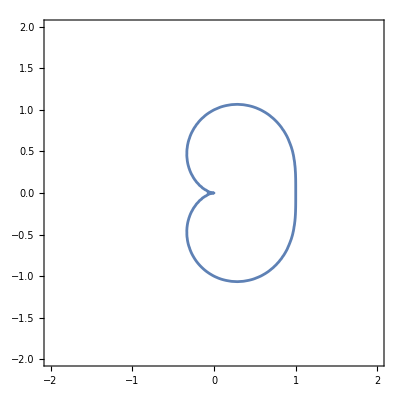

```mathematica
ContourPlot[(x^2+y^2)^2-y^2-x (x^2+y^2)==0,{x,-2,2},{y,-2,2}]
```

## 3. naloga [10 točk]

1. (5 točk) V spremenljivko potence shranite vse lihe potence števila 2 od 1 do 25, od katerih odštejete 1: 1, 7, 31, 127 ... Pomagajte si z ukazom Table.
2. (5 točk) Izberite vsa števila iz seznama potenc, ki so praštevila. Pomagajte si z ukazom Select.

```mathematica
potence=Table[2^(2n-1),{n,1,25}]
```

{2,8,32,128,512,2048,8192,32768,131072,524288,2097152,8388608,33554432,134217728,536870912,2147483648,8589934592,34359738368,137438953472,549755813888,2199023255552,8796093022208,35184372088832,140737488355328,562949953421312}

```mathematica
Select[potence,PrimeQ]
```

{2}